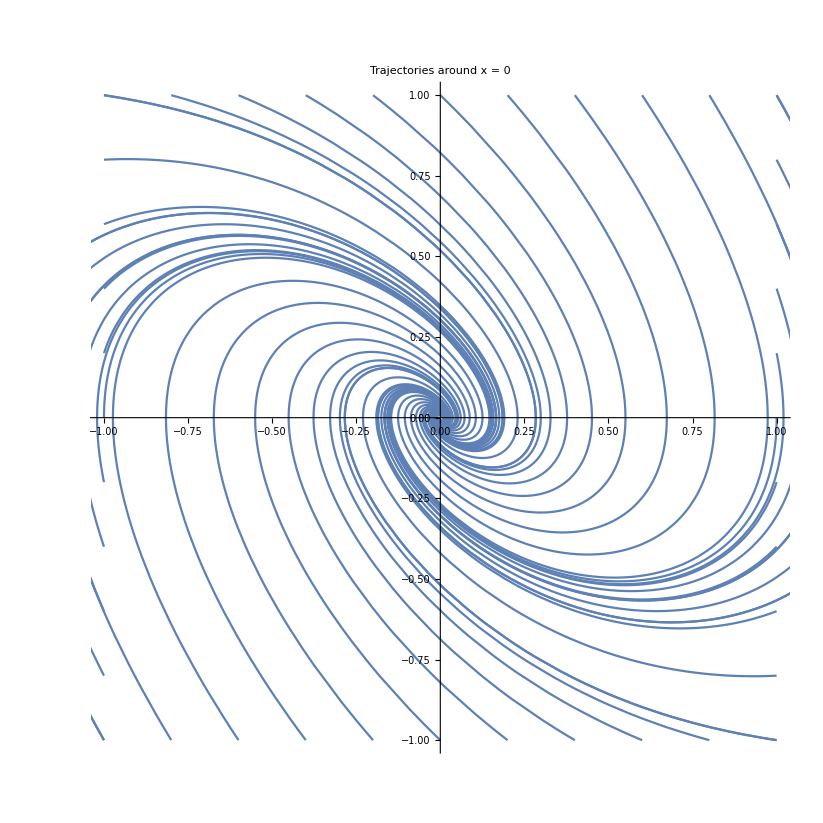

```mathematica
miny = -1;
maxy = 1;
xrangelength = maxy - miny;

step = 0.2;

sigma=1;

x0 = 0;
minx = x0 - xrangelength/2;
maxx = x0 + xrangelength/2;


sol[u_, v_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-sigma*y[t],x[0]==u,y[0]==v},{x,y},{t,10}]

Table1 = Table[{minx, y}, {y, miny, maxy, step}];
Table2 = Table[{x,maxy}, {x, minx, maxx, step}];
Table3 = Table[{maxx, y}, {y, miny, maxy,step}];
Table4 = Table[{x, miny}, {x, minx, maxx, step}];

TableFinal = Join[Table1,Table2,Table3,Table4];


Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,10},PlotRange->{{minx,maxx},{miny,maxy}},PlotLabel->Style["Trajectories around x = 0",FontSize->15]]/.Line[x_]:>{Arrowheads[{0., 0.01, 0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```

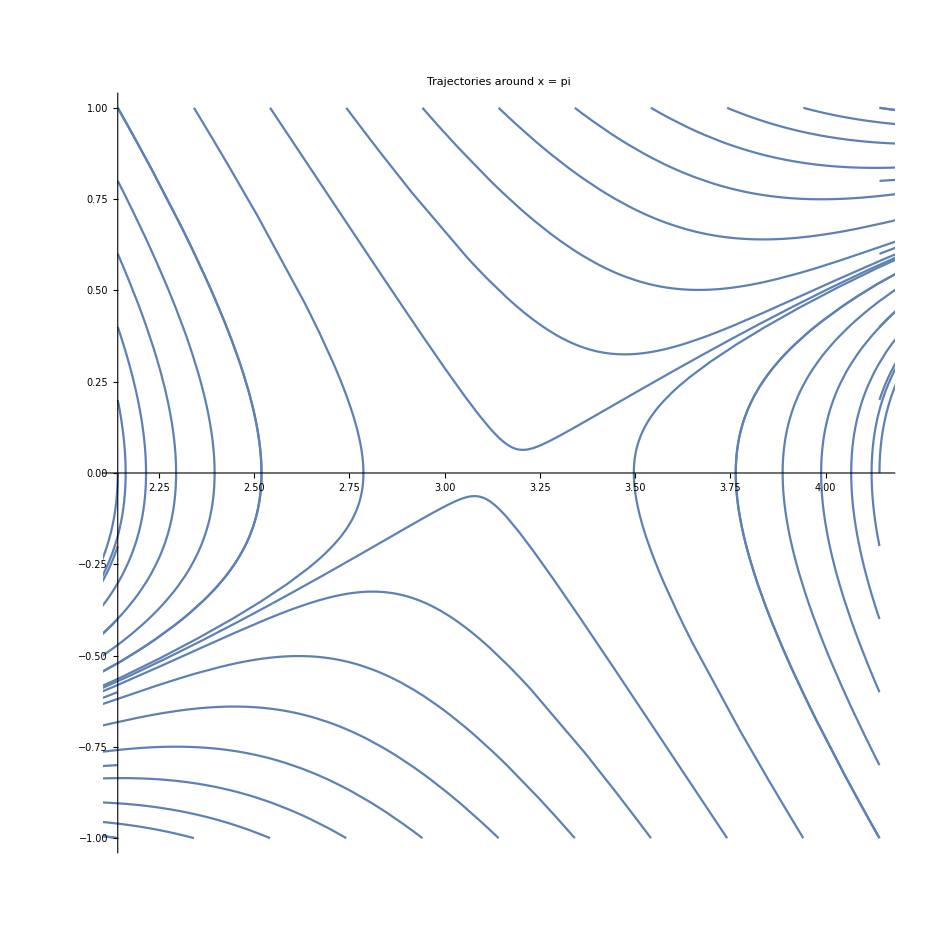

```mathematica
x0 = Pi;
minx = x0 - xrangelength/2;
maxx = x0 + xrangelength/2;


sol[u_, v_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-sigma*y[t],x[0]==u,y[0]==v},{x,y},{t,10}]

Table1 = Table[{minx, y}, {y, miny, maxy, step}];
Table2 = Table[{x,maxy}, {x, minx, maxx, step}];
Table3 = Table[{maxx, y}, {y, miny, maxy,step}];
Table4 = Table[{x, miny}, {x, minx, maxx, step}];

TableFinal = Join[Table1,Table2,Table3,Table4];


Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,10},PlotRange->{{minx,maxx},{miny,maxy}},PlotLabel->Style["Trajectories around x = pi",FontSize->15]]/.Line[x_]:>{Arrowheads[{0., 0.01, 0., 0., 0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```